```mathematica
β=2;ω0=2*Pi;
```

```mathematica
G[ω_]:=ω0^2/((ω0^2 - ω^2)+I*β*ω);
```

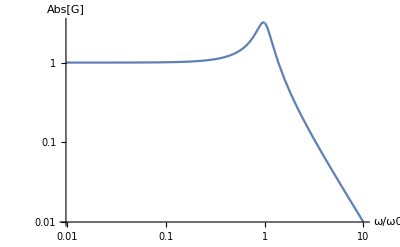

```mathematica
LogLogPlot[Abs[G[a*ω0]],{a,0,10}, PlotRange->Full, AxesLabel->{ω/"ω0",Abs[G]}]
```

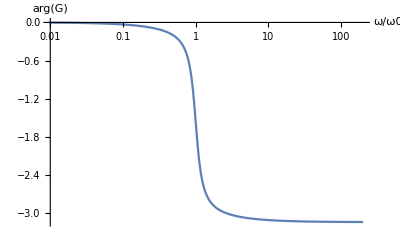

```mathematica
LogLinearPlot[Arg[G[a*ω0]],{a,0.01,200},AxesLabel->{ω/"ω0",Arg[G]},Exclusions->None]
```

```mathematica
Kd=0;Kp=10;Ki=1;β=2;ω0=2*Pi;
```

```mathematica
K[ω_]:=Kp-I*Ki/ω+I*Kd*ω;G[ω_]:=ω0^2/((ω0^2 - ω^2)+I*β*ω);T[ω_]:=G[ω]*K[ω]/(1+G[ω]*K[ω]);
```

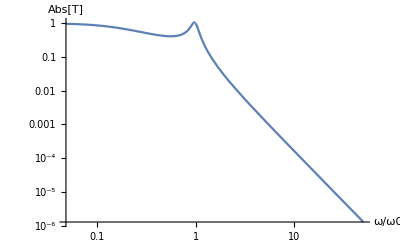

```mathematica
LogLogPlot[Abs[T[a*ω0]],{a,0,50},AxesLabel->{ω/"ω0",Abs[T]}]
```

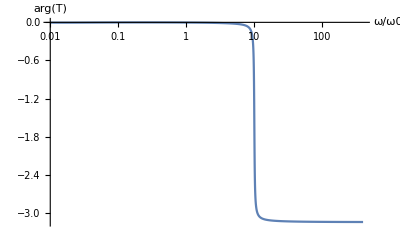

```mathematica
LogLinearPlot[Arg[T[a*ω0]],{a,0.01,400},PlotRange->Full,AxesLabel->{ω/"ω0",Arg[T]},Exclusions->None]
```

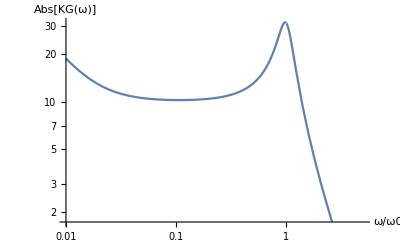

```mathematica
LogLogPlot[Abs[K[a*ω0]*G[a*ω0]],{a,0.01,5},AxesLabel->{ω/"ω0",Abs[KG[ω]]}]
```

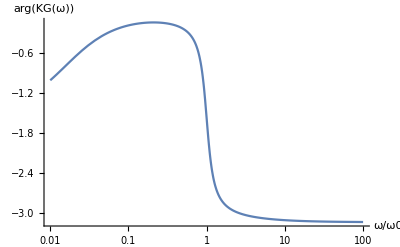

```mathematica
LogLinearPlot[Arg[K[a*ω0]*G[a*ω0]],{a,0.01,100},PlotRange->Full,AxesLabel->{ω/"ω0",Arg[KG[ω]]},Exclusions->None]
```

```mathematica
G[ω]
```

(4 π^2)/(4 π^2+2 ⅈ ω-ω^2)

```mathematica
(4 π^2)/(4 π^2+2 ⅈ ω-ω^2)*(4 π^2-2 ⅈ ω-ω^2)/(4 π^2-2 ⅈ ω-ω^2)
```

```mathematica
(4 π^2+2 ⅈ ω-ω^2)*(4 π^2-2 ⅈ ω-ω^2)//Simplify
```

16 π^4+4 ω^2-8 π^2 ω^2+ω^4

```mathematica
Sqrt[((4 π^2)((4 π^2-2 ⅈ ω-ω^2))/(16 π^4+4 ω^2-8 π^2 ω^2+ω^4))*(4 π^2)((4 π^2+2 ⅈ ω-ω^2))/(16 π^4+4 ω^2-8 π^2 ω^2+ω^4)]//Simplify
```

4 π^2 √(1/(16 π^4+4 ω^2-8 π^2 ω^2+ω^4))

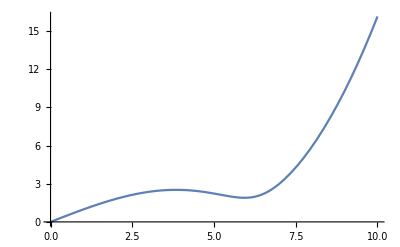

```mathematica
Plot[1/(4 π^2 √(1/(16 π^4+4 ω^2-8 π^2 ω^2+ω^4))/ω),{ω,0,10},PlotRange->Full]
```